```mathematica
Clear[predRfMonFPRTheor]; 

(* copying here *) 
predRfMonFPRTheor[detFNR_, dInProp_, pDetNCH0_:0(* for this context *)] := 1 -(1 - detFNR + pDetNCH0)^(dInProp+1);
```

```mathematica
(* detector FNR estimates for NCC *) 
N@predFNRfromData[fullStatefulTripleList[{4,5,6,7}, #], detFilenames]&/@ stWeightsDetAndPr
```

{0.10305,0.111555,0.113533,0.122315,0.128486,0.133075,0.143953,0.155505,0.160252,0.165829}

```mathematica
(* Bad ECC: our monitor FNR prediction based on the old FPR of 0.1*) 
N@predRfMonFPRTheor[0.1, 10]
```

0.686189

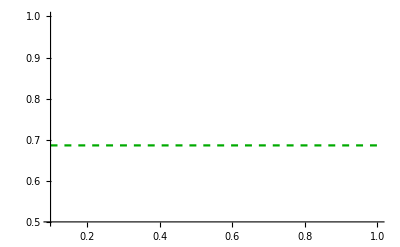

```mathematica
badStatefulECCChartRf = chartHorLine[predRfMonFPRTheor[0.1, 10],(*max-X*)1.8,0.1,Darker@Green, {Dashed},PlotRange->{{0.1,1},{0.5,1}}]
```

```mathematica
(* NCC: our monitor FNR prediction based on the new FPR *) 
N@predRfMonFPRTheor[predFNRfromData[fullStatefulTripleList[{4,5,6,7}, #], detFilenames], 10]&/@ stWeightsDetAndPr
```

{0.697691,0.72777,0.734363,0.761919,0.779698,0.792127,0.819086,0.844199,0.853566,0.863917}

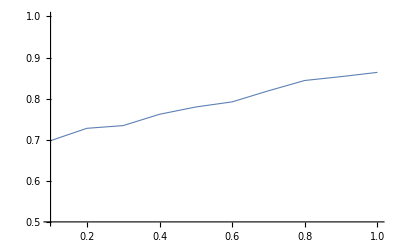

```mathematica
predStatefulFNRChartRf= ListLinePlot[Inner[List,  Range[0.1,1,0.1],predRfMonFPRTheor[predFNRfromData[fullStatefulTripleList[{4,5,6,7}, #], detFilenames], 10]&/@ stWeightsDetAndPr, List],PlotStyle->{ColorData[97,"ColorList"][[1]], Thickness[0.002]}, PlotRange->{{0.1,1},{0.5,1}}]
```

```mathematica
(* BBC: data-driven estimates of the FNR *)
```

```mathematica
(getMonValues[dataDirPathForSeshNumPostCorr[All], "FNR",#] & /@ stWeightsDetAndPr )// Flatten[#,1]&
```

{0.696893,0.684211,0.7026,0.700063,0.695625,0.718453,0.714014,0.772987,0.686113,0.715282}

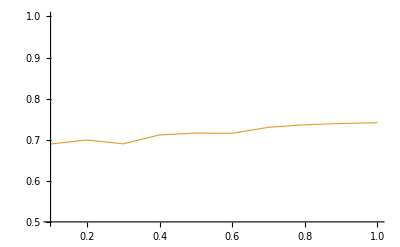

```mathematica
estStatefulFNRChartRf= ListLinePlot[Inner[List, Range[0.1,1,0.1],getMonValues[dataDirPathForSeshNumPostCorr[All], "FPR",#] & /@ stWeightsRf // Flatten[#,1]&, List],PlotStyle->{ColorData[97,"ColorList"][[2]], Thickness[0.002]}, PlotRange->{{0.1,1},{0.5,1}}]
```

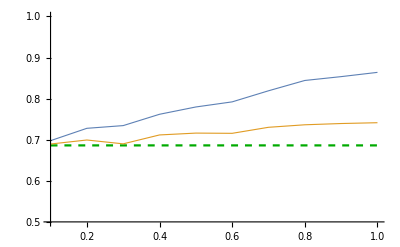

```mathematica
(* combination *) 
Show[badStatefulECCChartRf, predStatefulFNRChartRf, estStatefulFNRChartRf(*PlotRange->{{0.1,1},{0,1}}*)]
```